### Prepare

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/neutrino/MMA

```mathematica
imgSize=800;
```

## Effect of Gravitation

### Deflection of Light Around A Neutron Star

The equation for deflection angle of a tangent neutrino at z=rz with a impact parameter b is -θ=(2G M)/c^2 (∫_(-∞))^rz b/((z^2+b^2)^(3/2))dz-(2G M)/(b c^2)

```mathematica
2G M/c^2 Integrate[b/((z^2+b^2)^(3/2)),{z,-Infinity,rz},Assumptions->{z∈Reals,b∈Reals,rz∈Reals,rz>0,b≠0}]-2 G M/b/c^2//FullSimplify
```

(2 G M rz)/(b c^2 √(b^2+rz^2))

Check the dimension here. G M/b has the dimension Energy/Mass, So the overall dimension is 1 which is right.

We would like to see the effect of b and rz. The numerical value of 2GM/c^2 can be calculated.
Solar mass 1.988435×10^30 
Neutron star has about 1.4 Solar mass approximately
Gravitational constant 6.67×10^-11 newton square meters per kilogram squared

```mathematica
const2GMOc2=2 6.67×10^(-11) 1.4 1.988435×10^(30)/(9 10^16)
```

4126.22

Define a function of deflection angle

```mathematica
delta[b_,rz_]:=const2GMOc2 rz/√(b^2+rz^2)/b
```

```mathematica
Manipulate[Grid[{{Text["Impact Parameter in meters is" Style[b,Bold]],Text["Max z coordinate in Plot is" Style[rzMax,Bold]]},{LogLinearPlot[delta[b,rz],{rz,1000,rzMax},PlotRange->Full,Frame->True,FrameLabel->{"rz / m","delta / radian"},ImageSize->imgSize],SpanFromLeft}},Dividers->{False,2->True}],{{b,10000,"Impact Parameter"},1000,1000000},{{rzMax,1000000,"Plot Max Distance"},100000,100000000}]
```

```mathematica
Plot3D[delta[b,rz],{b,10000,100000},{rz,10000,100000},PlotRange->Full,AxesLabel->{"b","rz / m","delta / radian"},ImageSize->imgSize]
```

-Graphics3D-

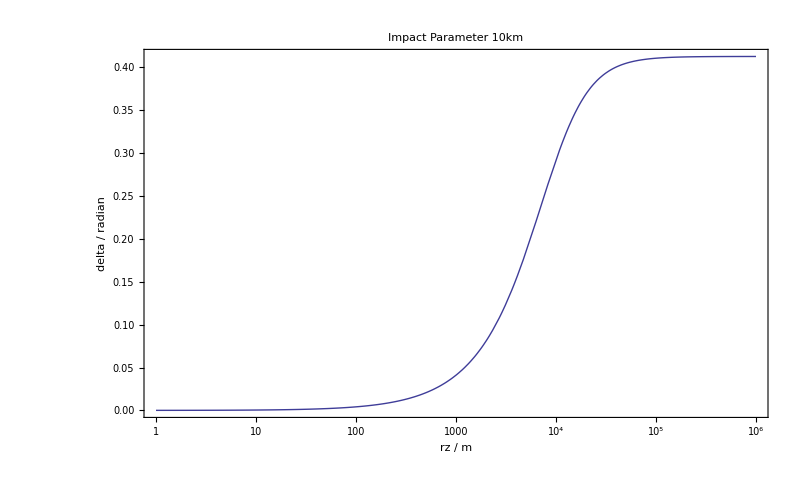

```mathematica
LogLinearPlot[delta[10000,rz],{rz,1,1000000},PlotRange->Full,Frame->True,FrameLabel->{"rz / m","delta / radian"},ImageSize->imgSize,PlotLabel->"Impact Parameter 10km"]
```

```mathematica
Export["deflectionAngle.png",%]
```

deflectionAngle.png